```mathematica
k[e_,m_]:=Sqrt[2*m*e]
```

```mathematica
hbarc=197.326968;
```

```mathematica
α[e_,v_,m_,r0_]:=Sqrt[2*m*(e+v)]
```

```mathematica
j[l_,x_]:=SphericalBesselJ[l,x]
dj[l_,x_]:=D[SphericalBesselJ[l,y],y] /. y->x
```

```mathematica
n[l_,x_]:=SphericalBesselY[l,x]
dn[l_,x_]:=D[SphericalBesselY[l,y],y] /. y->x
```

```mathematica
tandelta[e_,v_,m_,r0_,l_]:=
( α[e,v,m,r0]*dj[l,α[e,v,m,r0]*r0/hbarc]*j[l,k[e,m]*r0/hbarc]
-k[e,m]*dj[l,k[e,m]*r0/hbarc]*j[l,α[e,v,m,r0]*r0/hbarc])/
( α[e,v,m,r0]*dj[l,α[e,v,m,r0]*r0/hbarc]*n[l,k[e,m]*r0/hbarc]
-k[e,m]*dn[l,k[e,m]*r0/hbarc]*j[l,α[e,v,m,r0]*r0/hbarc])
```

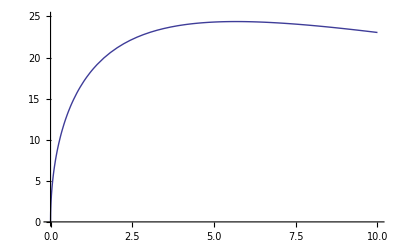

```mathematica
Plot[
180/Pi*ArcTan[tandelta[e,5,500,3,0]],
{e,0,10},
PlotRange->{0,25}]
```

```mathematica
listS1 = Table[
{e,180/Pi*ArcTan[tandelta[e,5,500,3,0]]},
{e,0.01,100,0.01}];
Export["listS1.dat",listS1,"Table"];
```

```mathematica
listP1 = Table[
{e,180/Pi*ArcTan[tandelta[e,5,500,3,1]]},
{e,0.01,100,0.01}];
Export["listP1.dat",listP1,"Table"];
```

```mathematica
listD1 = Table[
{e,180/Pi*ArcTan[tandelta[e,5,500,3,2]]},
{e,0.01,100,0.01}];
Export["listD1.dat",listD1,"Table"];
```

```mathematica
listF1 = Table[
{e,180/Pi*ArcTan[tandelta[e,5,500,3,3]]},
{e,0.01,100,0.01}];
Export["listF1.dat",listF1,"Table"];
```

```mathematica
listG1 = Table[
{e,180/Pi*ArcTan[tandelta[e,5,500,3,4]]},
{e,0.01,100,0.01}];
Export["listG1.dat",listG1,"Table"];
```

```mathematica
listH1 = Table[
{e,180/Pi*ArcTan[tandelta[e,5,500,3,5]]},
{e,0.01,100,0.01}];
Export["listH1.dat",listH1,"Table"];
```

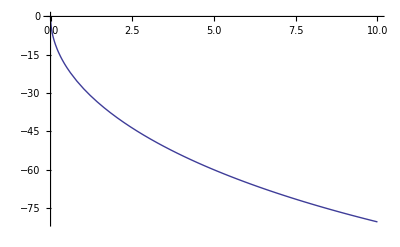

```mathematica
Plot[
180/Pi*ArcTan[tandelta[e,40,500,3,0]],
{e,0,10}]
```

```mathematica
listS2 = Table[
{e,180/Pi*ArcTan[tandelta[e,40,500,3,0]]},
{e,0.01,100,0.01}];
Export["listS2.dat",listS2,"Table"];
```